```mathematica
ClearAll["Global`*"]
$Assumptions = Element[{u, th, b1, b2, b3}, Reals];
(* symbolic operator labels*)
ClearAll[id, sx, sz, sxz, pmul];

(* sanity check*)
{id, sx, sz, sxz}
```

{id,sx,sz,sxz}

```mathematica
(* multiplication table of Paulis*)


pmul[id, a_] := {1, a};
pmul[a_, id] := {1, a};

pmul[sx, sx ] := {1, id};
pmul[sz, sz] := {1, id};

pmul[sz, sx ] := {-1, sxz};
pmul[sx, sz ] := {1, sxz};

pmul[sxz , sx ] := {-1, sz};
pmul[sx, sxz ] := {1, sz};

pmul[sxz, sz] := {1, sx};
pmul[sz, sxz ] := {-1, sx};

pmul[sxz, sxz ] := {-1, id};

(* sanity check*)
pmul[sz,sx]
pmul[sx,sz]
pmul[sxz,sx]
pmul[sx,sxz]
pmul[sxz,sz]
pmul[sz,sxz]
pmul[sxz,sxz]
```

{-1,sxz}

{1,sxz}

{-1,sz}

{1,sz}

{1,sx}

{-1,sx}

{-1,id}

```mathematica
(* Word multiplication  {sz, sz, sx}= Z_1 Z_2 X_3 *)

ClearAll[wordMultiply];

wordMultiply[w1_List, w2_List] :=Module[
{r1, r2, r3},

r1 = pmul[w1[[1]], w2[[1]]];
r2= pmul[w1[[2]], w2[[2]]];
r3 = pmul[w1[[3]], w2[[3]]];

{
r1[[1]] r2[[1]] r3[[1]], 
{r1[[2]], r2[[2]], r3[[2]]}
}
];

(* Sanity Check *)
Print[wordMultiply[{sz,sz,sx},{sz,sz,sx}]];
Print[wordMultiply[{sxz,id,id},{sx,id,id}]];
```

{1,{id,id,id}}

{-1,{sz,id,id}}

```mathematica
ClearAll[th, mx, mz, siteExp, cellExp];
(* m_x = \sin(2\theta) , m_z = -cos(2\theta) , <XZ>=0 *)

mx= Sin[2 th];
mz = -Cos[2 th];

siteExp[id] := 1;
siteExp[sx] := mx;
siteExp[sz] := mz;
siteExp[sxz] := 0;

cellExp[word_List]:= siteExp[word[ [ 1 ] ] ] siteExp[word [[2] ] ] siteExp[word [ [ 3] ]]; 

(* sanity Checks*)
Print[cellExp[{id, id, id}]];
Print[cellExp[{sz, sz, id}]];
Print[cellExp[{sz, sx, id}]];
Print[cellExp[{sxz, id, id}]];
```

1

Cos[2 th]^2

-Cos[2 th] Sin[2 th]

0

```mathematica
(* Operator sums representation {coefficient, word}  1-ub3 Z_1 Z_2 X_3 { {1, {id, id, id}}, {-u b3, {sz, sz, sx}} } *)
ClearAll[Ksym, u, b1, b2, b3];

(* 3 x 3 matrix*)
Ksym[ sgn_] :={
{  (* row 1*)
{
{1,{id,id,id}},{-sgn*u*b3,{sz,sz,sx}}
},
{
{sgn*u,{id,sz,sz}}
},
{
{sgn*u,{id,id,sz}}
}
},
{ (* row 2 *)
{
{-b1,{sx,id,id}}
},
{
{-sgn*u*b1,{sx,sz,sz}}
},
{
{-sgn*u *b1,{sx,id,sz}}
}
},
{ (* row 3 *)
{
{-b2,{sz,sx,id}}
},
{},
{
{-sgn*u *b2,{sz,sx,sz}}
}
}
};

(* K(u) and K(-u)*)
Kp = Ksym[1];
Km = Ksym[-1]; 

(* Sanity Checks*)

Print[Kp [[1,1]]];
Print[Km [[1,1]]];
Print[Kp[ [2,1]]];
Print[Km[ [2,1]]];
Print[Kp[ [3,2]]];
```

{{1,{id,id,id}},{-b3 u,{sz,sz,sx}}}

{{1,{id,id,id}},{b3 u,{sz,sz,sx}}}

{{-b1,{sx,id,id}}}

{{-b1,{sx,id,id}}}

{}

```mathematica
(* Multiplication of two operator sums  (1- ub3 A)(1+ ub3 A)= 1- u^2 b3^2 A^2 *)
ClearAll[opMultiply];

opMultiply[op1_List, op2_List] := Module[
{terms},
If[op1 === {} || op2 === {},  Return[{}]];

terms = Flatten[
Table[
Module[{res},
res = wordMultiply[op1[ [i, 2]], op2[ [j, 2]]  ];
{op1 [[i,1]] op2 [[j,1]] res [[1]], res[ [2]] }
],
{i, Length[op1]}, {j, Length[op2]}
],
1
];

terms
];

(* Sanity Check*)
test= opMultiply[ Km[ [1, 1]], Kp[ [1, 1]] ]
(* contract *)
Total[ (#[ [1]] cellExp[#[ [2]]] ) & /@ test ] // FullSimplify
```

{{1,{id,id,id}},{-b3 u,{sz,sz,sx}},{b3 u,{sz,sz,sx}},{-b3^2 u^2,{id,id,id}}}

1-b3^2 u^2

```mathematica
(* Building block for fourfold space tensor F_{\mu \nu}*)
ClearAll[opMultiplyMany];

opMultiplyMany[ops_List] := Fold[opMultiply, First[ops], Rest[ops]];

(* Sanity Check  F_00 = K_00(-u) K_00(u) K_00(u) K_00(-u)*)
test4 = opMultiplyMany[ {Km[ [1,1]] , Kp[ [1,1]], Kp[ [1,1]], Km[ [1,1]]}];
FullSimplify[Total[(# [ [1]] cellExp[#[ [2]]]) & /@  test4]]
```

(-1+b3^2 u^2)^2

```mathematica
(* Tensor sum contraction using FullSimplify *)

ClearAll[opContract];

opContract[op_List] := FullSimplify[
Total[ ( #[ [1]] cellExp[ #[ [2]]]) & /@ op]
];

(* Sanity Check F_00*)
opContract[test4]
```

(-1+b3^2 u^2)^2

```mathematica
(* Define Entries of F labeling set {0, 1, 2}for {0, x, z} *)

ClearAll[toPos];
toPos[n_Integer] := n + 1;

ClearAll[Fentry];

Fentry[in_List, out_List] := Module[
{a, b, c, d, e, f, g, h, A, B, C, D, op},

(* Tensor indices *)
{a, b, c, d} = in;
{e, f, g, h} = out;
A= Km[ [toPos[a], toPos[e] ]];
B= Kp[ [toPos[b], toPos[f] ]];
C= Kp[ [toPos[c], toPos[g] ]];
D= Km[ [toPos[d], toPos[h] ]];

op = opMultiplyMany[{A,B, C, D}];

opContract[op]
];

(* Sanity Check*)
 Fentry[{0,0, 0, 0}, {0, 0, 0, 0}]
```

(-1+b3^2 u^2)^2

```mathematica
(* Flattening with base 3 (effective spin 1 system ) *)
ClearAll[decodeIndexRev,encodeIndexRev];

decodeIndexRev[n_Integer]:=Reverse[IntegerDigits[n,3,4]];
encodeIndexRev[list_List]:=FromDigits[Reverse[list],3];


(* Sanity Check*)
decodeIndexRev /@ {0, 1, 2, 3, 80}
encodeIndexRev[{0,0, 0, 1}]
encodeIndexRev[{2,2, 2, 2}]
```

{{0,0,0,0},{1,0,0,0},{2,0,0,0},{0,1,0,0},{2,2,2,2}}

27

80

```mathematica
(*Flat entries in terms of \mu and \nu*)

ClearAll[FentryFlat];

FentryFlat[mu_Integer, nu_Integer] := FentryFlat[mu, nu] = Module[
{in, out},
in= decodeIndexRev[mu];
out = decodeIndexRev[nu];
Fentry[in, out]
];
(* Sanity Check*)
Table[decodeIndexRev[n], {n, 0, 5}]
FentryFlat[0, 0]
FentryFlat[0, 1]
FentryFlat[0, 2]
FentryFlat[0, 3]
```

{{0,0,0,0},{1,0,0,0},{2,0,0,0},{0,1,0,0},{1,1,0,0},{2,1,0,0}}

(-1+b3^2 u^2)^2

u (-1+b3^2 u^2) Cos[2 th]^2

u (1-b3^2 u^2) Cos[2 th]

u (1-b3^2 u^2) Cos[2 th]^2

```mathematica
(*Build the full matrix F *)

ClearAll[Fmat];

Fmat = Table[
FentryFlat[mu, nu],
{mu, 0, 80},
{nu, 0, 80}
];
(* Sanity Check *)
Dimensions[Fmat]
Fmat [[1,1]]
Fmat [[1,2]]
Fmat [[1,3]]
Fmat [[1,4]]
```

{81,81}

(-1+b3^2 u^2)^2

u (-1+b3^2 u^2) Cos[2 th]^2

u (1-b3^2 u^2) Cos[2 th]

u (1-b3^2 u^2) Cos[2 th]^2

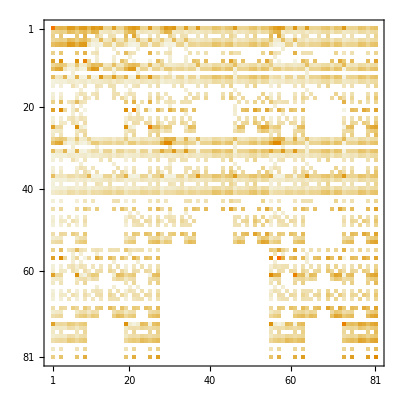

{41.9031+0.000175968 ⅈ,41.9031-0.000175968 ⅈ,41.903+0. ⅈ,25.9988+32.8621 ⅈ,25.9988-32.8621 ⅈ,41.9028+0. ⅈ,28.9856+7.91786 ⅈ,28.9856-7.91786 ⅈ,28.9856+7.91786 ⅈ,28.9856-7.91786 ⅈ}

```mathematica
(* Diagonalization tests *)

rulesStag= {b1 -> 1, b2 -> Sqrt[2], b3 -> Sqrt[3]};

(* Apply rule simplification to the F matrix*)
FmatStag = FullSimplify[Fmat /. rulesStag];

(* only numbers F *)
ClearAll[Fnum];
Fnum[u0_,th0_]:=N[Fmat/. rulesStag/. {u->u0,th->th0}];
M=Fnum[0.5 Pi,1.8];

MatrixPlot[Abs[M]]
Take[Eigenvalues[M],10]
```

```mathematica
(*Exact support pattern exploration --> map to a graph *)
eps=10^-12;
supportNum=Unitize[Chop[Abs[M],eps]];

Dimensions[supportNum]
MatrixQ[supportNum]

gUnd=AdjacencyGraph[
supportNum,
DirectedEdges->False,
VertexLabels->"Name"];

blocksUnd=ConnectedComponents[gUnd];
Length/@blocksUnd
```

{81,81}

True

{81}

StronglyConnectedComponents[0]

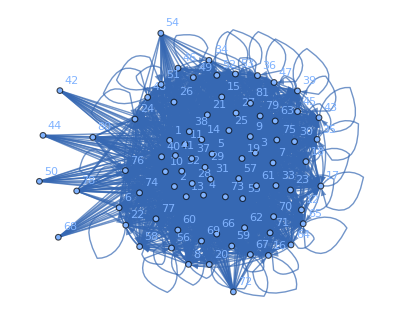
StronglyConnectedComponents[{1+decodeIndexRev[-Graphics-],decodeIndexRev[-Graphics-],decodeIndexRev[-Graphics-],decodeIndexRev[-Graphics-]}]

```mathematica
gDir=AdjacencyGraph[
Transpose[supportNum],
DirectedEdges->True,
VertexLabels->"Name"];

scc=StronglyConnectedComponents[gDir];
Length/@scc

blockLabels[block_]:=decodeIndexRev/@(block-1);
blockLabels/@Take[scc,UpTo[10]]
```

```mathematica
(*Chain length/polynomial size entering RootsAndNorms*)
Clear[RootsAndNorms];
RootsAndNorms[M_,αβγvec_]:= Module[
{L,S,α,β,γ,coeffs,b,ϕ,x,y,
P,vlist,u,v,k,s,nrm,rootsData
        },

L = M;
S = Floor[(M+2)/3];

{α, β, γ} =αβγvec;
coeffs = Flatten[Table[{α, β, γ} ,{i, 1, M+1}]][[1;;2M]];
Clear[b];
Table[b[m] = Sqrt[coeffs[[m]]],{m, 1, 2M}];

Clear[ϕ, x, y];
ϕ[-1, u_]:=0;
ϕ[0, u_]:=0;
Table[
ϕ[i_, u_] :=ArcSin[ - u b[i] /(Cos[ϕ[i-2, u]]Cos[ϕ[i-1, u]])];
x[i_, u_] := Cos[ϕ[i, u]];
y[i_, u_] := Sin[ϕ[i, u]];
,{i, 1, 2 M}];

AbsoluteTiming[
idS = IdentityMatrix[S+1];
shiftMat =idS[[Join[{S+1},Range[1, S]]]];
Clear[Pc,Pcprev];
Table[
Pcprev[m] = SparseArray[{1->1}, {S+1}] // Normal;
,{m, -2, 0}];
Table[
temp = Pcprev[m-1] - b[m]^2shiftMat. Pcprev[m-3];
If[m<=M,
Pc[m] = temp;
Pcprev[m] = Pc[m];
];
,{m, 1, M}];
Clear[P];
P[v_]:= Pc[M].Table[v^(s-1), {s, 1, S+1}]//FullSimplify ;
vlist=Sort[v/. NSolve[P[v]==0,v,50]][[-S;;]];
Table[
v[k]= vlist[[k]];
{u[k], u[-k]} = {Sqrt[v[k]],-Sqrt[v[k]]};
,{k, 1, S}];
ulist = Sqrt[vlist]
];

Clear[PP,PPder];
PP[M,u_]:= Pc[M].Table[u^(2s-2), {s, 1, S+1}];
PP[M-1,u_]:= Pc[M-1].Table[u^(2s-2), {s, 1, S+1}];
PPder[M,u_]:= Pc[M].Table[(2s-2) u^(2s-2-1), {s, 1, S+1}];
normlist= Table[
Ν[s] = 16 PP[M-1,u[s]]Product[1-u[s]^2/u[i]^2,{i,1,s-1}]Product[1-u[s]^2/u[i]^2,{i,s+1,S}]  
,{s, 1, S}]  // Sqrt // Abs;
Return[Transpose[{ulist, normlist}]]
];
```

```mathematica
(* Block 1: Definitions *)
ClearAll[Fmat];

Fmat=Table[
FentryFlat[mu,nu],
{mu,0,80},
{nu,0,80}];
```

```mathematica
(* Parameters *)
rulesStag={b1->1,b2->Sqrt[2],b3->Sqrt[3]};
Msys=80;       (*example*)
th0=0.1 Pi;
ktest= 1;
wp=60;
```

```mathematica
(*Block 2: roots and norms*)
rootsData=RootsAndNorms[Msys,{1,2,3}];

uList=rootsData[[All,1]];
NkList=rootsData[[All,2]];
NkSqList=NkList^2;

Length[uList]
(*rootsData[[ktest;;Min[1,Length[rootsData]]]]*)
```

27

{81,81}

True

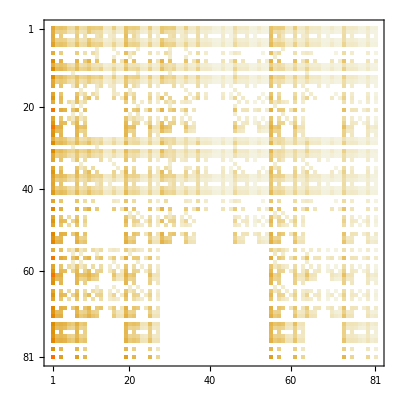

```mathematica
(* Block 3: Build the normalized transfer block *)
ClearAll[FrawNum];

FrawNum[k_Integer,th0_,wp_:50]:=N[
Fmat/. rulesStag/. {u->uList [[k]],th->th0},
wp];



Atest=FrawNum[ktest,th0,wp];
Dimensions[Atest]
MatrixQ[Atest,NumericQ]
MatrixPlot[Abs[Atest]]
```

```mathematica
(*Block 4: Spectrum *)

ClearAll[RightSpec];

RightSpeck[k_Integer, th0_, wp_: 50] := Module[
{A, vals, vecs, ord},
A = FrawNum[k,th0, wp];
{vals, vecs} = Eigensystem[A];
ord = Ordering[Abs[vals], All,  Greater];
<|
"vals" ->vals[ [ord]],
"vecs" -> (Normalize /@ vecs[ [ord]])
|>
];
```

```mathematica
(*Block 5: spectrum powers *)
ClearAll[PoweredNormalizedVals];

PoweredNormalizedVals[k_Integer,th0_,Msys_Integer,wp_:50]:=Module[
{spec,vals,Nk2},
spec=RightSpeck[k,th0,wp];
vals=spec["vals"];
Nk2=NkSqList [[k]];
vals^(Msys-2)/Nk2
];
(* checks *)
spec1=RightSpeck[ktest,th0,wp];

Take[Abs[spec1["vals"]],81]
Take[PoweredNormalizedVals[ktest,th0,Msys,wp],15]
```

{0.0831254,0.0831148,0.0831148,0.0831148,0.0831095,0.0831095,0.0617716,0.0617716,0.0617716,0.0617716,0.0105443,0.0105443,0.0105443,0.0105443,0.0105443,0.0105443,0.0105443,0.0105443,0.00935564,0.00935564,0.00935161,0.00935161,0.00935155,0.00935155,0.00934766,0.00934766,0.00190491,0.00190491,0.00105219,4.74821×10^-16,2.29807×10^-16,2.29807×10^-16,2.18692×10^-16,2.18692×10^-16,1.7626×10^-16,1.7626×10^-16,1.09058×10^-16,1.03019×10^-16,6.41605×10^-17,6.41605×10^-17,6.34936×10^-17,5.6997×10^-17,5.6997×10^-17,4.70988×10^-17,4.70988×10^-17,2.95436×10^-17,2.95436×10^-17,2.55383×10^-17,2.19603×10^-17,2.19603×10^-17,1.59705×10^-17,1.59705×10^-17,1.57187×10^-17,1.4036×10^-17,1.4036×10^-17,1.31126×10^-17,8.99083×10^-18,7.66549×10^-18,7.66549×10^-18,6.41348×10^-18,5.00573×10^-18,5.00573×10^-18,2.26316×10^-18,2.26316×10^-18,1.34586×10^-18,1.34586×10^-18,4.74297×10^-31,1.98929×10^-32,1.98929×10^-32,7.66159×10^-33,3.43441×10^-33,7.71946×10^-34,7.39517×10^-34,0.,0.,0.,0.,0.,0.,0.,0.}

General::munfl: (-4.74821×10^-16)^78 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (1.69092×10^-16-1.55626×10^-16 ⅈ)^78 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (1.69092×10^-16+1.55626×10^-16 ⅈ)^78 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{1.08831×10^-60,4.60055×10^-61+9.74326×10^-61 ⅈ,4.60055×10^-61-9.74326×10^-61 ⅈ,1.07748×10^-60,1.07206×10^-60-9.29238×10^-63 ⅈ,1.07206×10^-60+9.29238×10^-63 ⅈ,7.72621×10^-71+5.57669×10^-71 ⅈ,7.72621×10^-71-5.57669×10^-71 ⅈ,7.72621×10^-71+5.57669×10^-71 ⅈ,7.72621×10^-71-5.57669×10^-71 ⅈ,1.23874×10^-130,1.23874×10^-130,1.23874×10^-130,1.23874×10^-130,-1.23874×10^-130-1.09684×10^-143 ⅈ}

```mathematica
(*Block6 : stable diagnostic*)

ClearAll[LogPoweredNormalizedAbsVals];

LogPoweredNormalizedAbsVals[k_Integer,th0_,Msys_Integer,wp_:50]:=Module[
{spec,vals,Nk2},spec=RightSpeck[k,th0,wp];
vals=spec["vals"];
Nk2=NkSqList[[k]];
(Msys-2) Log[Abs[vals]]-Log[Abs[Nk2]]
];

Take[LogPoweredNormalizedAbsVals[ktest,th0,Msys,wp],27]
```

{-138.066,-138.08,-138.08,-138.08,-138.088,-138.088,-161.229,-161.229,-161.229,-161.229,-308.47,-308.47,-308.485,-308.485,-308.486,-308.486,-308.499,-308.499,-432.592,-432.592,-478.89,-2938.13,-2938.13,-2979.68,-3010.15,-3010.15,-3053.}